```mathematica
S = ToExpression["50000 - \\frac{500000}{x+10} - 2x",TeXForm]
```

50000-2 x-500000/(10+x)

```mathematica
Sp=ToExpression["\\frac{500000}{(x+10)^2} - 2",TeXForm]
```

-2+500000/(10+x)^2

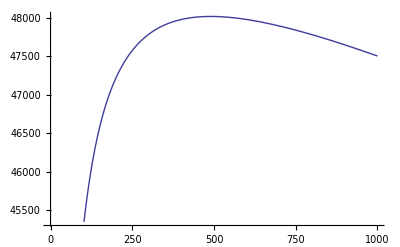

```mathematica
Plot[S,{x,0,1000}]
```

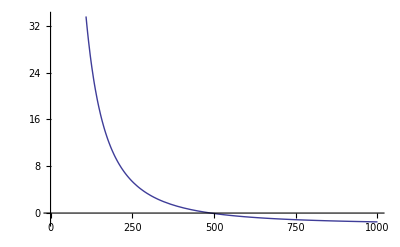

```mathematica
Plot[Sp,{x,0,1000}]
```

```mathematica
f=ToExpression["\\frac{4}{x}+x^4",TeXForm]
```

```mathematica
4/x+x^4
```

```mathematica
fp=ToExpression["4x^3 - 4/x^2",TeXForm]
```

-4/x^2+4 x^3

```mathematica
Needs["PlotLegends`"]
```

```mathematica
Plot[{f,fp},{x,-2,2},PlotLegend->{"f(x)=4/x+x^4","f'(x)=-4/x^2+4 x^3"}]
```